```mathematica
dummy[a_,b_, r_]:=Module[{a1=a, b1=b, r1=r},
SeedRandom[r1];
Thread[{{a1,b1}->{Sqrt[a1^2 +b1^2]+1000RandomReal[{-0.1,0.1}]}}]
];
```

```mathematica
data=Table[dummy[i,j,222],{i,1,10,0.2},{j,1,10,0.2}];
data2=Flatten[data];
s=Dimensions[data2][[1]]
```

2116

```mathematica
trainingdata=data2[[;;Ceiling[0.8*s]]];
validationdata=data2[[Ceiling[0.8*s]+1;;s]];
```

```mathematica
f=NetChain[{DotPlusLayer[12],64,Tanh,32,1},"Input"->2]
f=NetInitialize[f];
```

NetChain[<>]

```mathematica
trainedData=NetTrain[f,trainingdata]
```

NetChain[<>]

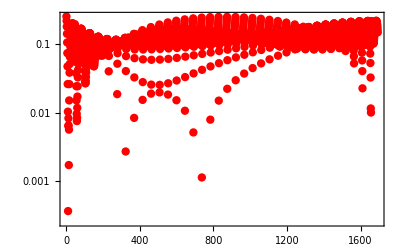

```mathematica
ListLogPlot[(trainedData/@trainingdata[[All,1]]-trainingdata[[All,2]])*100/trainingdata[[All,2]]//Flatten//Abs,Frame->True,FrameStyle->Black,PlotStyle->{Red,PointSize->0.015}]
```